```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0};
```

```mathematica
df[ζ_]=k (1+d^2/ζ^2)^(θ/π);
f[ζ_]=c+ k(ζ/d)^(1-2 θ/π)  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-ζ^2/d^2];
(*f[ζ_]=∫df[ζ]ⅆζ+c//Simplify*)
```

```mathematica
(*Limit[f[ϵ],ϵ->0,Direction->-1]//Simplify*)
```

```mathematica
(*Limit[f[ϵ-ⅈ d],ϵ->0,Direction->-1]//Simplify*)
```

```mathematica
(*k=((-ⅈ c+dz) ⅇ^(-ⅈ θ) √π)/(d Gamma[(π+θ)/π] Gamma[1/2-θ/π]);  before absorbing const in k*)


c=-(dz+du) Tan[θ]+ⅈ du;
k=(π √π)/(π-2 θ)((dz-ⅈ c) ⅇ^(-ⅈ θ))/(Gamma[1+θ/π] Gamma[1/2-θ/π]);
(*Re[c]+Re@ k(L/d)^(1-2 θ/π)  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-L^2/d^2]=L*)
```

```mathematica
d=L((Re[k]  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-L^2/(dz+du)^2])/(L-Re[c]))^(1/(1-2 θ/π));
{Block[{dz=.6,du = .1,L=50,θ =20*π/180},f[50]],Block[{dz=.6,du = .1,L=50,θ =-20*π/180},f[50]]}
```

{51.9401+0.1 ⅈ,51.6132+0.1 ⅈ}

```mathematica
d=L(Re[k](L/(dz+du))^(-2 θ/π)  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-L^2/(dz+du)^2])/(L-Re[c]);
{Block[{dz=.6,du = .6,L=50,θ =20*π/180},f[50]],Block[{dz=.6,du = .1,L=50,θ =-20*π/180},f[50]]}
```

{49.9375+0.6 ⅈ,49.9587+0.1 ⅈ}

```mathematica
d=L(Re[k](L/dz)^(-2 θ/π)  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-L^2/dz^2])/(L+dz Tan[θ]);
{Block[{dz=.6,du = .6,L=50,θ =20*π/180},f[50]],Block[{dz=.6,du = .1,L=50,θ =-20*π/180},f[50]]}
```

{49.9666+0.6 ⅈ,49.965+0.1 ⅈ}

d = dz + du; (* if scaling the two domains with eachother *)

d = 1;  (* if simplifying expression *)

```mathematica
Block[{dz=.6,du = .1,L=50,θ =20*π/180},{f[.00001],f[-ⅈ d+.000001]}]
```

{-0.25463+0.1 ⅈ,2.17709×10^-7-0.6 ⅈ}

{49.9632+0.0000702904 ⅈ,49.9587+0.0000888896 ⅈ}

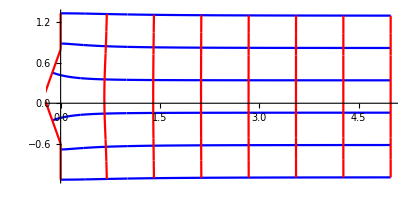

```mathematica
Block[{dz=.6,du = .1,L=20,θ =20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

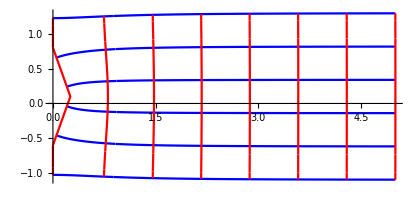

```mathematica
Block[{dz=.6,du = .1,L=20,θ =-20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```